```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

NOCUTS

```mathematica
(*namerun="Mtt300"*)
namerun="nocuts"
```

nocuts

```mathematica
Nreq=100000;
```

```mathematica
namefolder="mupem_to_nunuttbar_2to4"
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000

etal=coeff[prova[5],Nreq/Nreals];
Mll =coeff[prova[14],Nreq/Nreals];
Mtt =coeff[prova[15],Nreq/Nreals];
etat=coeff[prova[10],Nreq/Nreals];
```

mupem_to_nunuttbar_2to4

100000

```mathematica
namefolder="WW_ttbar_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000;
MttZZ =coeff[prova[10],Nreq/Nreals];
etatZZ=coeff[prova[6],Nreq/Nreals];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000(*84142*);
MttZZmuhalf =coeff[prova[10],Nreq/Nreals];
etatZZmuhalf=coeff[prova[6],Nreq/Nreals];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000;
MttZZmuquarter =coeff[prova[10],Nreq/Nreals];
etatZZmuquarter=coeff[prova[6],Nreq/Nreals];




NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000;
MttZZmuLePDF =coeff[prova[10],Nreq/Nreals];
etatZZmuLePDF=coeff[prova[6],Nreq/Nreals];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000;
MttZZmuhalfLePDF =coeff[prova[10],Nreq/Nreals];
etatZZmuhalfLePDF=coeff[prova[6],Nreq/Nreals];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000(*88899*);
MttZZmuquarterLePDF =coeff[prova[10],Nreq/Nreals];
etatZZmuquarterLePDF=coeff[prova[6],Nreq/Nreals];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZptmu =prova[10];
etatZZptmu=prova[6];*)
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"2to4_noQED","ttbar Eva mu=sqrtshat","ttbar Eva mu=sqrtshat/2","ttbar Eva mu=sqrtshat/4", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotlegend2={"2to4_noQED", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV";
```

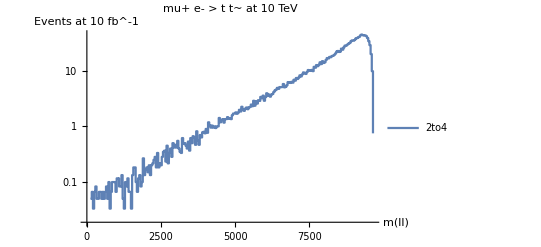

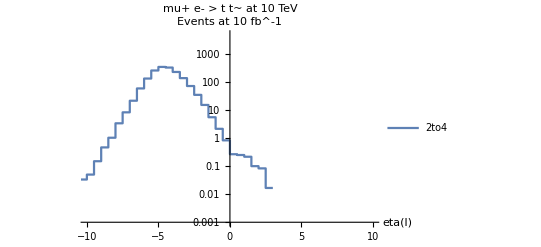

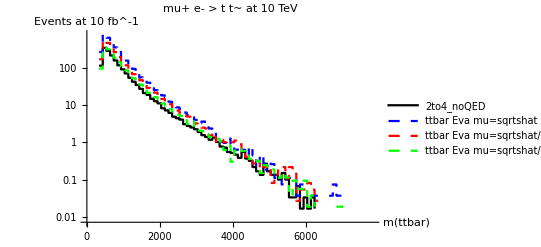

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

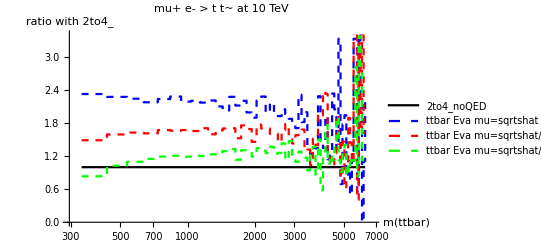

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

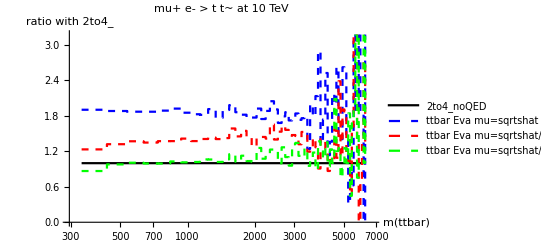

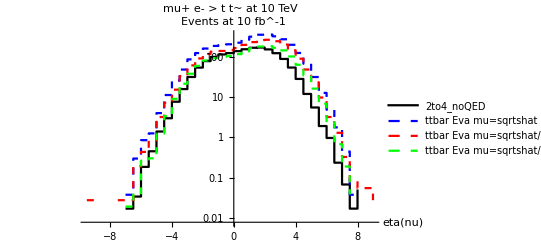

```mathematica
ListLogPlot[{joinbin[Mll,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etal,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

(*ListLogPlot[{joinbin[ptt,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] *)


ListLogPlot[{joinbin[Mtt,10],joinbin[MttZZ,10],joinbin[MttZZmuhalf,10],joinbin[MttZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[Mtt,10],joinbin[Mtt,10]],rapp[joinbin[MttZZ,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuhalf,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuquarter,10],joinbin[Mtt,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}] 

ListLogLinearPlot[{rapp[joinbin[Mtt,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuLePDF,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuhalfLePDF,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuquarterLePDF,10],joinbin[Mtt,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}] 





ListLogPlot[{etat,etatZZ,etatZZmuhalf,etatZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

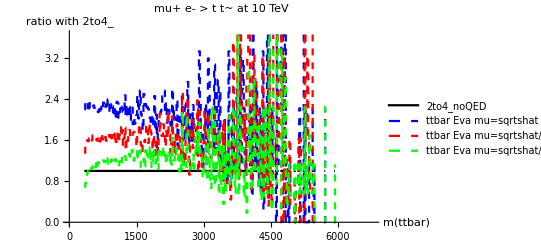

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

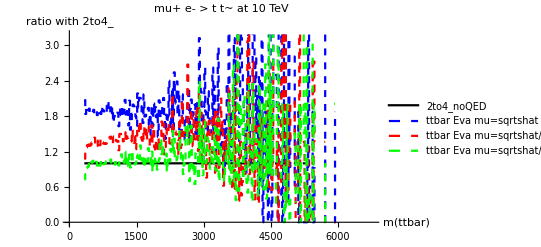

```mathematica
rebinning=2;
ListPlot[{rapp[joinbin[Mtt,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZ,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuhalf,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuquarter,rebinning],joinbin[Mtt,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}] 

ListPlot[{rapp[joinbin[Mtt,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuLePDF,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuhalfLePDF,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuquarterLePDF,rebinning],joinbin[Mtt,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}]
```

```mathematica
Plus@@Map[#[[2]]&,etatZZmuquarterLePDF]*100000/77261
Plus@@Map[#[[2]]&,etatZZmuhalfLePDF]
Plus@@Map[#[[2]]&,etatZZmuLePDF]
```

2178.39

2284.21

3138.68

M(ttbar)>500 GeV con anche Pt(t)> 150 GeV e |etat| < 2.5.

```mathematica
(*namerun="Mtt300"*)
namerun="MWW500_ptnu150_eta2half"
```

MWW500_ptnu150_eta2half

```mathematica
Nreq=100000;
```

```mathematica
namefolder="mupem_to_nunuttbar_2to4"
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000

etal=coeff[prova[5],Nreq/Nreals];
Mll =coeff[prova[14],Nreq/Nreals];
Mtt =coeff[prova[15],Nreq/Nreals];
etat=coeff[prova[10],Nreq/Nreals];
```

mupem_to_nunuttbar_2to4

100000

```mathematica
namerun="Mtt500_ptt150_eta2half"
```

Mtt500_ptt150_eta2half

```mathematica
namefolder="WW_ttbar_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000;
MttZZ =coeff[prova[10],Nreq/Nreals];
etatZZ=coeff[prova[6],Nreq/Nreals];
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalf"<>"/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalf"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000;
MttZZmuhalf =coeff[prova[10],Nreq/Nreals];
etatZZmuhalf=coeff[prova[6],Nreq/Nreals];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarter"<>"/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarter"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000(*86531*);
MttZZmuquarter =coeff[prova[10],Nreq/Nreals];
etatZZmuquarter=coeff[prova[6],Nreq/Nreals];




NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000;
MttZZmuLePDF =coeff[prova[10],Nreq/Nreals];
etatZZmuLePDF=coeff[prova[6],Nreq/Nreals];


NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000(*96333*);
MttZZmuhalfLePDF =coeff[prova[10],Nreq/Nreals];
etatZZmuhalfLePDF=coeff[prova[6],Nreq/Nreals];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
Nreals=100000(*77261*);
MttZZmuquarterLePDF =coeff[prova[10],Nreq/Nreals];
etatZZmuquarterLePDF=coeff[prova[6],Nreq/Nreals];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZptmu =prova[10];
etatZZptmu=prova[6];*)
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"2to4_noQED","ttbar Eva mu=sqrtshat","ttbar Eva mu=sqrtshat/2","ttbar Eva mu=sqrtshat/4", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotlegend2={"2to4_noQED", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV";
```

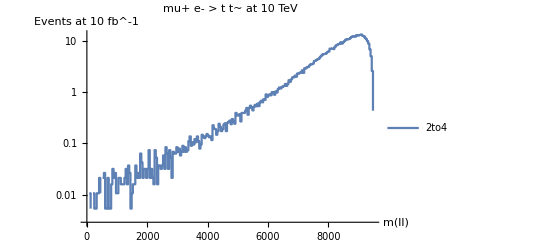

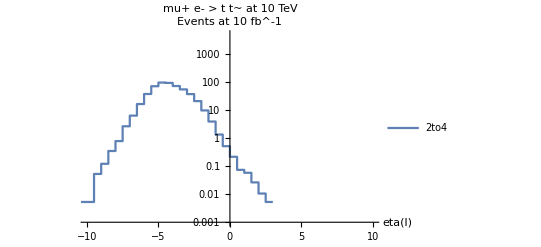

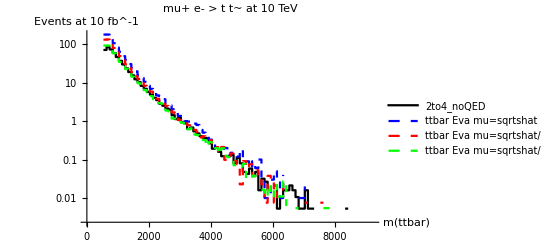

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

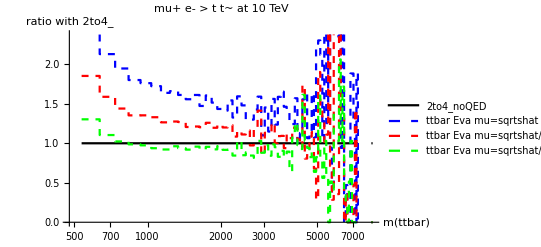

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

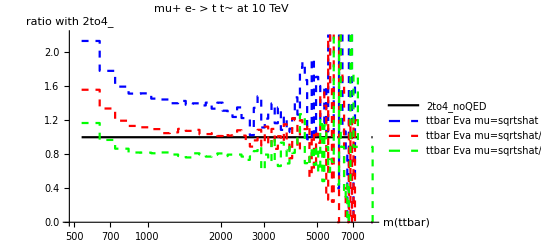

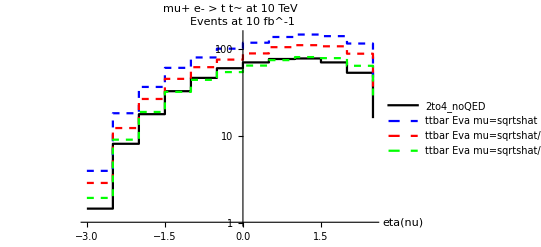

```mathematica
ListLogPlot[{joinbin[Mll,4]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotLabel->plotlabel,AxesLabel->{"m(ll)","Events at 10 fb^-1"}] 

ListLogPlot[{joinbin[etal,1]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend0,PlotStyle->plotstyle0,PlotRange->{{-10,10},{10^-3,5000}},PlotLabel->plotlabel,AxesLabel->{"eta(l)","Events at 10 fb^-1"}] 

(*ListLogPlot[{joinbin[ptt,2]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,PlotRange->{{0,1000},{10,1000}},AxesLabel->{"pt(nu)","Events at 10 fb^-1"}] *)


ListLogPlot[{joinbin[Mtt,10],joinbin[MttZZ,10],joinbin[MttZZmuhalf,10],joinbin[MttZZmuquarter,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","Events at 10 fb^-1"}] 

ListLogLinearPlot[{rapp[joinbin[Mtt,10],joinbin[Mtt,10]],rapp[joinbin[MttZZ,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuhalf,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuquarter,10],joinbin[Mtt,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}] 

ListLogLinearPlot[{rapp[joinbin[Mtt,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuLePDF,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuhalfLePDF,10],joinbin[Mtt,10]],rapp[joinbin[MttZZmuquarterLePDF,10],joinbin[Mtt,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}] 





ListLogPlot[{etat,etatZZ,etatZZmuhalf,etatZZmuquarter},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(nu)","Events at 10 fb^-1"}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

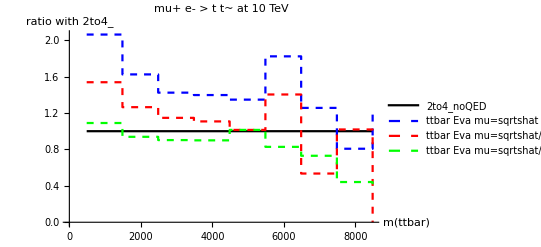

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

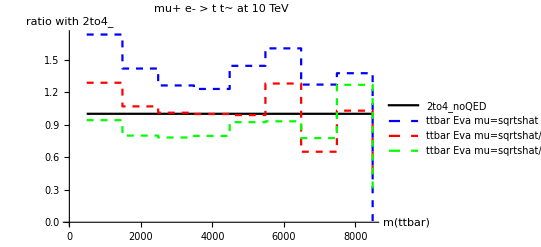

```mathematica
rebinning=100;
ListPlot[{rapp[joinbin[Mtt,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZ,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuhalf,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuquarter,rebinning],joinbin[Mtt,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}] 

ListPlot[{rapp[joinbin[Mtt,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuLePDF,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuhalfLePDF,rebinning],joinbin[Mtt,rebinning]],rapp[joinbin[MttZZmuquarterLePDF,rebinning],joinbin[Mtt,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_"}]
```

```mathematica
Plus@@Map[#[[2]]&,etatZZmuquarterLePDF]*100000/77261
Plus@@Map[#[[2]]&,etatZZmuhalfLePDF]
Plus@@Map[#[[2]]&,etatZZmuLePDF]
```

607.925

635.562

848.867